Nathan Magari
805505312
natemagari@g.ucla.edu
HW4

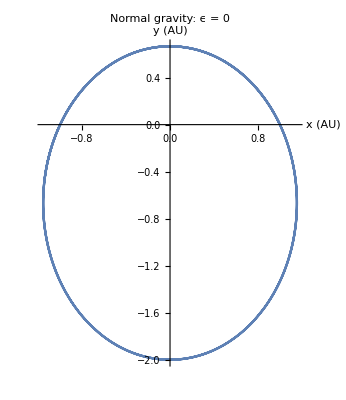

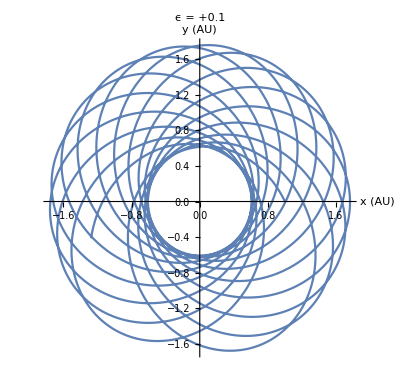

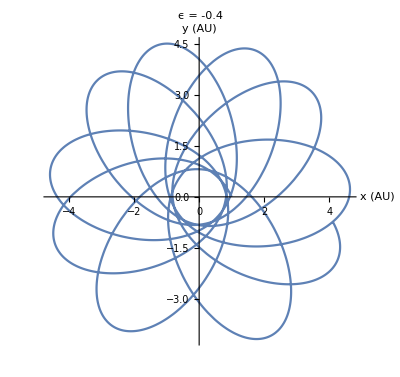

```mathematica
(*PROBLEM I*)
Remove["Global`*"]//Quiet
(*SETUP EQUATIONS OF MOTION*)
SetAttributes[m,Constant];
U := -4 Pi^2 m / r[t]^(1+e);
T := 0.5 m(x'[t]^2+y'[t]^2);
lag:=T-U;
x[t_]:= r[t]Cos[θ[t]];
y[t_] := r[t]Sin[θ[t]];
EL[q_] := D[lag,q] - Dt[D[lag,D[q,t]],t] ==0;
ellist := {EL[θ[t]],EL[r[t]]}//FullSimplify;
iclist := {θ[0]==0,r[0]==1,θ'[0] == 2Pi, r'[0] ==-Pi};
eqnlist := Join[ellist,iclist]
(*PARAMETERS and PLOTS*)
m = 1;(*doesn't really matter*)
(*i (Normal Gravity)*)
e=0;
thi = 5;
soln1 =NDSolve[eqnlist,{θ,r},{t,0,thi},MaxSteps->Infinity];
ParametricPlot[{x[t],y[t]}/.soln1,{t,0,thi},PlotLabel->"Normal gravity: ϵ = 0",AxesLabel->{"x (AU)","y (AU)"}]

(*ii*)
e = 0.1;
thi = 20;
soln2 =NDSolve[eqnlist,{θ,r},{t,0,thi},MaxSteps->Infinity];
ParametricPlot[{x[t],y[t]}/.soln2,{t,0,thi},PlotLabel->"ϵ = +0.1",AxesLabel->{"x (AU)","y (AU)"}]

(*iii*)
e=-0.4;
thi = 40;
soln3 =NDSolve[eqnlist,{θ,r},{t,0,thi},MaxSteps->Infinity];
ParametricPlot[{x[t],y[t]}/.soln3,{t,0,thi},PlotLabel->"ϵ = -0.4",AxesLabel->{"x (AU)","y (AU)"}]
```

```mathematica
(*PROBLEM II*)
(*i (Normal Gravity)*)
thi = 5;
sun1 = Graphics[{Yellow,PointSize[0.15],Point[{0,0}]}];
earth1[t_] := Graphics[{Blue,PointSize[0.06],Point[{x[t],y[t]}/.soln1]}];
line1[t_]:=Graphics[{Red,Line[{{0.01,0.01},{x[t],y[t]}}/.soln1]}];
traj1[t_]:= ParametricPlot[{x[s],y[s]}/.soln1,{s,Max[0,t-2],t+0.01}];
pix1[t_]:= Show[sun1,earth1[t],traj1[t],line1[t],PlotRange->{{-2,2},{-3,1}},AspectRatio->Automatic, Axes->True,PlotLabel->"Normal gravity: ϵ = 0",AxesLabel->{"x (AU)","y (AU)"}];
Animate[pix1[t],{t,0,thi},AnimationRunning ->False,AnimationRunTime->20]


(*ii*)
thi = 20;
sun2 = Graphics[{Yellow,PointSize[0.15],Point[{0,0}]}];
earth2[t_] := Graphics[{Blue,PointSize[0.06],Point[{x[t],y[t]}/.soln2]}];
line2[t_]:=Graphics[{Red,Line[{{0,0},{x[t],y[t]}}/.soln2]}];
traj2[t_]:= ParametricPlot[{x[s],y[s]}/.soln2,{s,Max[0,t-6],t+0.01}];
pix2[t_]:= Show[sun2,earth2[t],line2[t], traj2[t],PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic, Axes->True,PlotLabel->"ϵ = +0.1",AxesLabel->{"x (AU)","y (AU)"}];
Animate[pix2[t],{t,0,thi},AnimationRunning ->False,AnimationRunTime->20]


(*iii*)
thi = 40;
sun3 = Graphics[{Yellow,PointSize[0.05],Point[{0,0}]}];
earth3[t_] := Graphics[{Blue,PointSize[0.02],Point[{x[t],y[t]}/.soln3]}];
line3[t_]:=Graphics[{Red,Line[{{0,0},{x[t],y[t]}}/.soln3]}];
traj3[t_]:= ParametricPlot[{x[s],y[s]}/.soln3,{s,Max[0,t-20],t+0.01}];
pix3[t_]:= Show[sun3,earth3[t],line3[t], traj3[t],PlotRange->3{{-2,2},{-2,2}},AspectRatio->Automatic, Axes->True,PlotLabel->"ϵ = -0.4",AxesLabel->{"x (AU)","y (AU)"}];
Animate[pix3[t],{t,0,thi},AnimationRunning ->False,AnimationRunTime->20]
```

```mathematica
(*PROBLEM III*)
Remove["Global`*"]//Quiet
(*SETUP EQUATIONS OF MOTION*)
SetAttributes[{G,m1,m2},Constant];
r1[t_]={x1[t],y1[t]};
r2[t_]={x2[t],y2[t]};
dist[a_,b_] = √((a-b).(a-b));
U = - G m1 m2 / dist[r1[t],r2[t]];
T = 0.5 m1 r1'[t].r1'[t] + 0.5m2 r2'[t].r2'[t];
lag=T-U;
EL[q_] := D[lag,q] - Dt[D[lag,D[q,t]],t] ==0;
ellist = {EL[x1[t]],EL[y1[t]],EL[x2[t]],EL[y2[t]]}//FullSimplify;
iclist = {x1[0]==20,y1[0]==10,x2[0]== 0, y2[0] ==0,x1'[0]==-1,y1'[0]==0,x2'[0]== 0, y2'[0] ==0};
eqnlist = Join[ellist,iclist];


(*Frames*)
rcm[t_] := (m1 r1[t]+ m2 r2[t])/(m1+m2);
(*PARAMETERS and PLOTS*)
G=1;
m1=10;
m2=15;
thi = 200;
soln = NDSolve[eqnlist,{x1,x2,y1,y2},{t,0,thi},MaxSteps->50000][[1]];

(*LAB*)
p1[t_] := Graphics[{Blue,PointSize[0.025],Point[r1[t]/.soln]}]
p2[t_] := Graphics[{Red,PointSize[0.0375],Point[r2[t]/.soln]}]
pcm[t_] := Graphics[{Black,Point[rcm[t]/.soln]}]
traj1[t_] :=ParametricPlot[r1[s]/.soln,{s,0,t+0.01}];
traj2[t_]:=ParametricPlot[r2[s]/.soln,{s,0,t+0.01}];
trajcm[t_] :=ParametricPlot[rcm[s]/.soln,{s,0,t+0.01}];
pix[t_]:= Show[p1[t],p2[t],pcm[t],traj1[t],traj2[t],trajcm[t],PlotRange->{{-70,20},{-35,35}},AspectRatio->Automatic, Axes->True,PlotLabel->"Lab frame",AxesLabel->{"x","y"}];
Animate[pix[t],{t,0,thi},AnimationRunning ->False,AnimationRunTime->20]
(*CM*)
p1cm[t_] := Graphics[{Blue,PointSize[0.05],Point[{r1[t]-rcm[t]}/.soln]}]
p2cm[t_] := Graphics[{Red,PointSize[0.075],Point[{r2[t]-rcm[t]}/.soln]}]
pcmcm[t_] := Graphics[{Black,Point[{0,0}/.soln]}]
traj1cm[t_] :=ParametricPlot[{r1[s]-rcm[s]}/.soln,{s,0,t+0.01}];
traj2cm[t_]:=ParametricPlot[{r2[s]-rcm[s]}/.soln,{s,0,t+0.01}];
pixcm[t_]:= Show[p1cm[t],p2cm[t],pcmcm[t],traj1cm[t],traj2cm[t],PlotRange->{{-25,25},{-25,25}},AspectRatio->Automatic, Axes->True,PlotLabel->"COM Frame",AxesLabel->{"x","y"}];
Animate[pixcm[t],{t,0,thi},AnimationRunning ->False,AnimationRunTime->20]
```